```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/c++/seminar"];
```

```mathematica
Oscillator=Import["oscillator.dat"];
```

```mathematica
xList=Oscillator.{{1,0},{0,1},{0,0}};
```

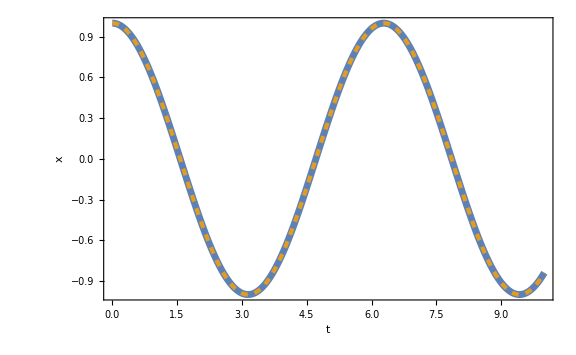

```mathematica
Show[ListPlot[xList,FrameLabel->{t,x},PlotLegends->Placed[LineLegend[{"num"},LegendMarkerSize->30],{0.87,0.8}],PlotStyle->AbsoluteThickness[5]],Plot[Cos[t],{t,0,10},PlotStyle->{Color[2],Dashed,AbsoluteThickness[3]},PlotLegends->Placed[LineLegend[{"cos t"},LegendMarkerSize->30],{0.87,0.8}]]]
```

```mathematica
Osc2=Import["2oscillator.dat"];
```

```mathematica
xList=Osc2.{{1,0},{0,1},{0,0},{0,0},{0,0}};
yList=Osc2.{{1,0},{0,0},{0,0},{0,1},{0,0}};
```

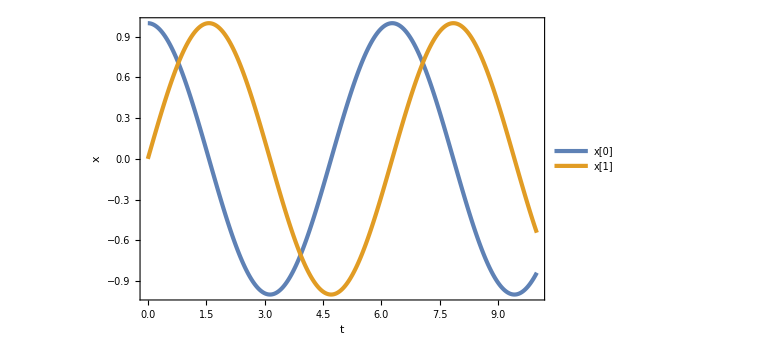

```mathematica
ListPlot[{xList,yList},FrameLabel->{t,x},PlotLegends->Placed[{"x[0]","x[1]"},{0.1,0.2}]]
```

```mathematica
DCbg=Import["double_chaotic_bg.dat"];
```

```mathematica
phiList=Map[{#[[6]],#[[2]]}&,DCbg];
psiList=Map[{#[[6]],#[[4]]}&,DCbg];
psivsphi=Map[{#[[2]],#[[4]]}&,DCbg];
HList=Map[{#[[6]],#[[7]]}&,DCbg];
eList=Map[{#[[6]],#[[8]]}&,DCbg];
```

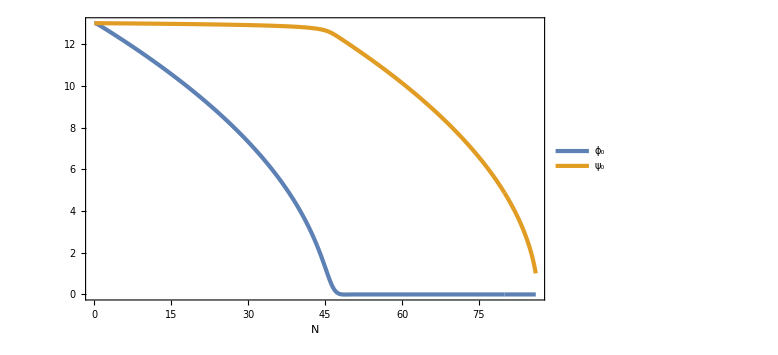

```mathematica
ListPlot[{phiList,psiList},FrameLabel->{N,None},PlotLegends->Placed[{Subscript[ϕ, 0],Subscript[ψ, 0]},{0.2,0.2}]]
```

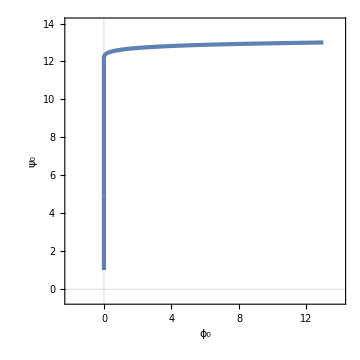

```mathematica
ListPlot[psivsphi,FrameLabel->{Subscript[ϕ, 0],Subscript[ψ, 0]},PlotRange->{{-2,14},{-0.5,14}},AspectRatio->1,GridLines->{{0},{0}},Axes->False,ImageSize->Medium]
```

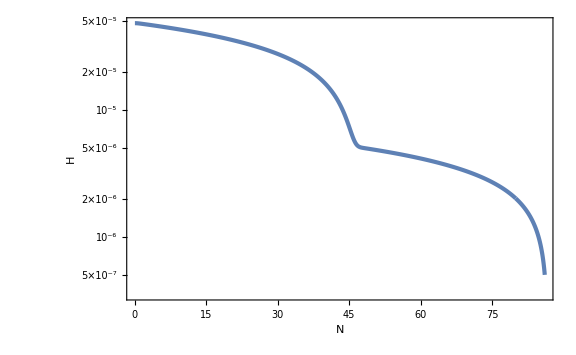

```mathematica
ListLogPlot[HList,FrameLabel->{N,H}]
```

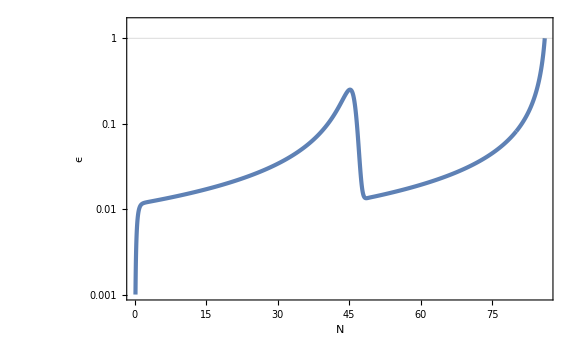

```mathematica
ListLogPlot[eList,FrameLabel->{N,ϵ},GridLines->{None,{1}},PlotRange->{0.001,1.5}]
```

```mathematica
DCptb=Import["double_chaotic_ptb.dat"];
```

```mathematica
phiList=Map[{#[[6]],#[[2]]}&,DCptb];
psiList=Map[{#[[6]],#[[4]]}&,DCptb];
HList=Map[{#[[6]],#[[7]]}&,DCptb];
aHList=Map[{#[[6]],#[[7]]Exp[#[[6]]]}&,DCptb];
eList=Map[{#[[6]],#[[8]]}&,DCptb];
calPR1List=Map[{#[[6]],#[[9]]}&,DCptb];
calPR2List=Map[{#[[6]],#[[10]]}&,DCptb];
calPR3List=Map[{#[[6]],#[[11]]}&,DCptb];
calPR4List=Map[{#[[6]],#[[12]]}&,DCptb];
calPR5List=Map[{#[[6]],#[[13]]}&,DCptb];
```

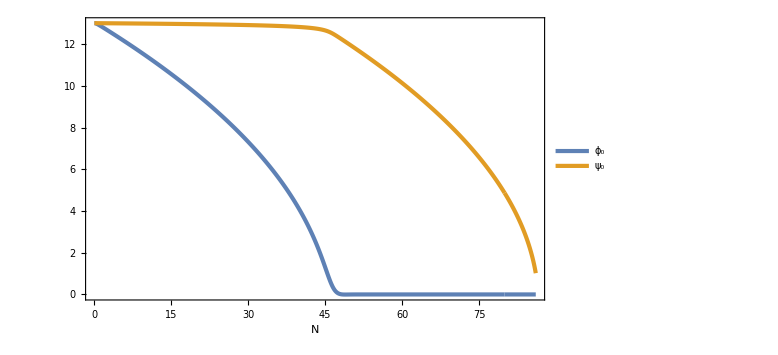

```mathematica
ListPlot[{phiList,psiList},FrameLabel->{N,None},PlotLegends->Placed[{Subscript[ϕ, 0],Subscript[ψ, 0]},{0.2,0.2}]]
```

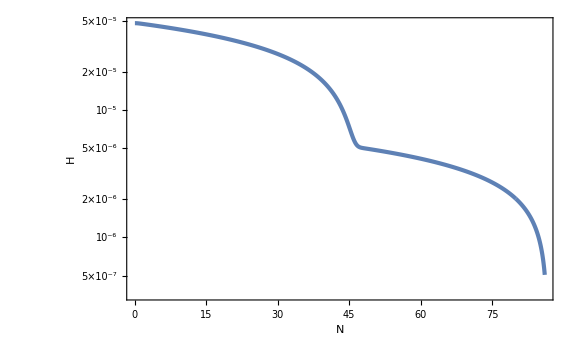

```mathematica
ListLogPlot[HList,FrameLabel->{N,H}]
```

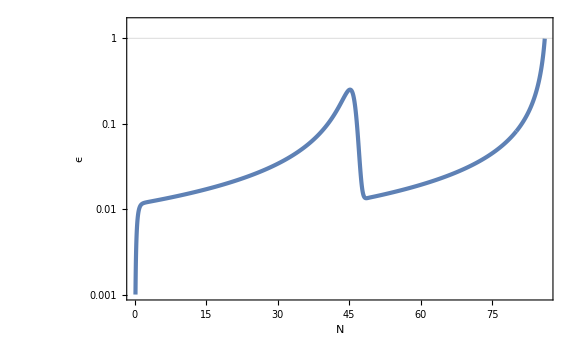

```mathematica
ListLogPlot[eList,FrameLabel->{N,ϵ},GridLines->{None,{1}},PlotRange->{0.001,1.5}]
```

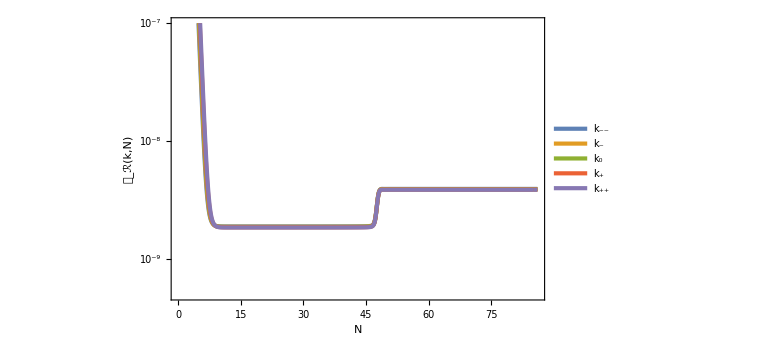

```mathematica
ListLogPlot[{calPR1List,calPR2List,calPR3List,calPR4List,calPR5List},PlotRange->{5 10^-10,10^-7},FrameLabel->{N,Subscript[𝒫, ℛ][k,N]},PlotLegends->Placed[LineLegend[{Subscript[k, "--"],Subscript[k, "-"],Subscript[k, 0],Subscript[k, "+"],Subscript[k, "++"]},LegendLayout->{"Row",2}],{0.7,0.75}]]
```

```mathematica
Last[calPR1List][[2]]
Last[calPR2List][[2]]
Last[calPR3List][[2]]
Last[calPR4List][[2]]
Last[calPR5List][[2]]
```

3.93229×10^-9

3.90957×10^-9

3.90194×10^-9

3.88173×10^-9

3.86983×10^-9

```mathematica
dlnk=0.1;
LastcalPRList={{Exp[-2dlnk],Last[calPR1List][[2]]},{Exp[-dlnk],Last[calPR2List][[2]]},{1,Last[calPR3List][[2]]},{Exp[dlnk],Last[calPR4List][[2]]},{Exp[2dlnk],Last[calPR5List][[2]]}};
LogLogcalPRList=Map[{Log[#[[1]]],Log[#[[2]]]}&,LastcalPRList];
```

```mathematica
fit=FindFit[LogLogcalPRList,a x+b,{a,b},x]
```

{a→-0.0391692,b→-19.3625}

```mathematica
1+a/.fit
LastcalPRfit[k_]=Exp[b] k^a/.fit;
```

0.960831

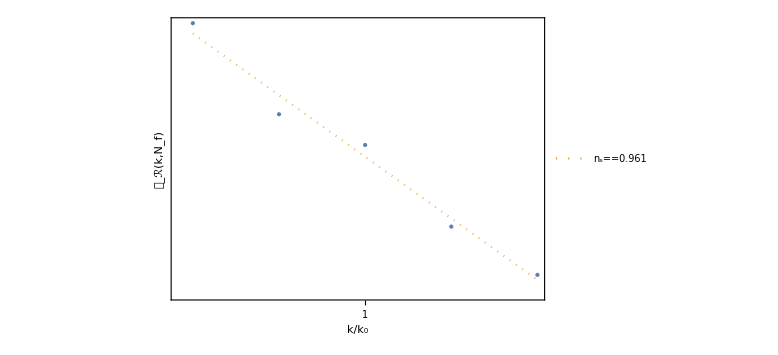

```mathematica
Show[ListLogLogPlot[LastcalPRList,Joined->False,PlotStyle->Directive[PointSize->Large],FrameLabel->{"k/k_0",Subscript[𝒫, ℛ][k,Subscript[N, "f"]]}],LogLogPlot[LastcalPRfit[k],{k,Exp[-2dlnk],Exp[2dlnk]},PlotStyle->{Color[2],Dotted},PlotLegends->Placed[{Subscript[n, "s"]==0.961},{0.75,0.8}]]]
```

```mathematica
Hi=HList[[1,2]]
k0=10^3 Hi;
```

0.000048059

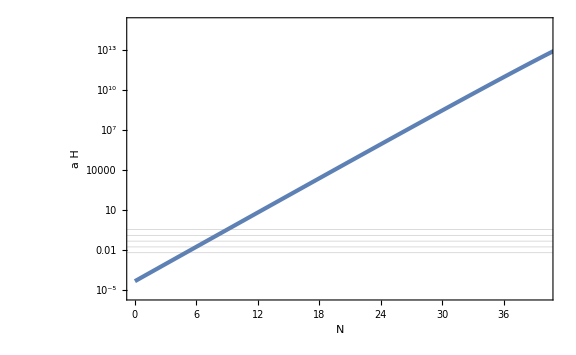

```mathematica
ListLogPlot[aHList,GridLines->{None,{k0 Exp[-2dlnk],k0 Exp[-dlnk],k0,k0 Exp[dlnk],k0 Exp[2dlnk]}},PlotRange->{{0,40},{0.1Hi,10^15}},FrameLabel->{N,a H}]
```

```mathematica
aHint[NN_]=Interpolation[aHList][NN];
```

```mathematica
N0=NN/.FindRoot[aHint[NN]==k0,{NN,10}]
```

6.98851

```mathematica
Hint[NN_]=Interpolation[HList][NN];
H0=Hint[N0]
```

0.0000443304

```mathematica
((H0/(2π))^2/8)/(Last[calPR3List][[2]])
```

0.00159468